## Scattering from a Spherical Square Well

## Preliminaries

In this notebook, we compute the phase shifts of the potential with V = -V0 for r<R and V=0 for r>R with an analytic formula and using the Variable Phase Approach (VPA). The reduced mass is μ.

Work in units where ℏ=1 and we measure mass in units of μ and lengths in terms of R.  Thus we set μ and R to 1. However, we will continue to make them explicit in the formulas.

```mathematica
μ = 1; R=1.;
```

The only parameter to adjust now is the depth V0.

```mathematica
Vsw[r_,V0_] := -V0 HeavisideTheta[R-r]  (* Define the square well *)
```

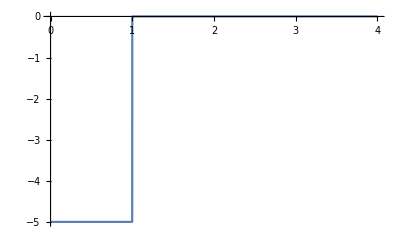

```mathematica
Plot[Vsw[r,5],{r,0,4},Exclusions->None]  (* Uncomment to check potential *)
```

```mathematica
Ek[k_] := k^2/(2μ)   (* Convenient definition of kinetic energy *)
```

## Analytic result for the phase shift

Use the formula for δ(E) from one of the problems, converting it to δ(k) using Ek(k):

```mathematica
deltaAnalytic[k_,V0_] := ArcTan[Sqrt[Ek[k]/(Ek[k]+V0)] Tan[R Sqrt[2μ(Ek[k]+V0)]]]-R Sqrt[2 μ Ek[k]]
deltaAnalytic1[k_,V0_]:=ArcTan[Sqrt[Ek[k]/(Ek[k]+V0)]Tan[R Sqrt[2μ(Ek[k]+V0)]]]
deltaAnalytic2[k_,V0_]:=R Sqrt[2 μ Ek[k]]
```

Use Cell->Convert  to->TraditionalForm to get it in a form easier to check we have entered it correctly:
deltaAnalytic(k_,V0_):=tan^-1(√((Ek(k))/(Ek(k)+V0)) tan(R √(2 μ (Ek(k)+V0))))-R √(2 μ Ek(k))

Always check that the function actually produces a number.

```mathematica
deltaAnalytic[5,0.5]
```

-6.17727

```mathematica
deltaAnalytic1[5,0.5]
```

-1.17727

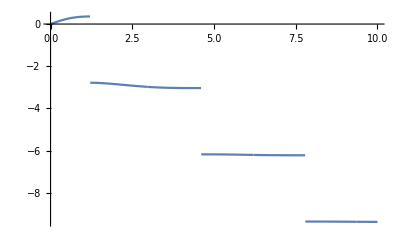

```mathematica
Plot[deltaAnalytic[k,0.5],{k,0,10}]
```

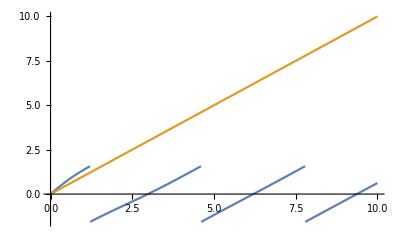

```mathematica
Plot[{deltaAnalytic1[k,0.5],deltaAnalytic2[k,0.5]},{k,0,10}]
```

What is going on with the steps?  Why are they there?  Is the phase shift really discontinuous?  How would you fix it?

Here is one “fix” that makes the result continuous for this example, but we will still have issues when V0 is large enough to support bound states.

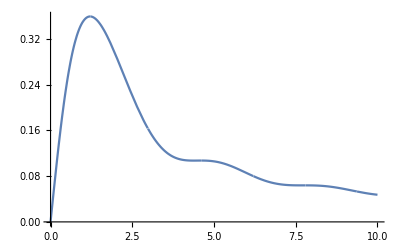

```mathematica
Plot[ArcTan[Tan[deltaAnalytic[k,0.5]]],{k,0,10}]
```

```mathematica
deltaAnalyticAdjusted[k_,V0_] := ArcTan[Tan[deltaAnalytic[k,V0]]]
```

We can also avoid this issue by looking at k Cot[δ(k)] instead, which doesn’t have these ambiguities.

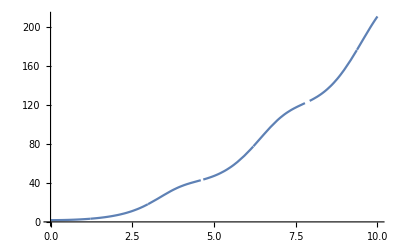

```mathematica
Plot[k Cot[deltaAnalytic[k,0.5]],{k,0,10}]
```

## Phase shift from the Variable Phase Approach

Use the formula: deltarho'(r)==-(2 μ Vsw(r) sin^2(deltarho(r)+k r))/k with the initial condition that deltarho(0) = 0.

We’ll need a numerical differential equation solver.  In Mathematica this is NDSolve:

```mathematica
?NDSolve
```

In principle we integrate out to infinity.  In practice, we choose a value of k and integrate out to Rmax, chosen to be well beyond the range of the potential (at which point the right side of the equation for deltarho’(r) is zero), and then evaluate deltarho(Rmax), which is the phase shift for momentum k.  Here is an implementation:

```mathematica
deltaVPA[k_,V0_] :=(
Rmax = 10; (* integrate out to Rmax; just need Rmax > R for square well *)ans = NDSolve[{deltarho'[r]==-(1/k)2μ Vsw[r,V0] Sin[k r + deltarho[r]]^2,deltarho[0]==0},deltarho,{r,0,Rmax},AccuracyGoal->6,PrecisionGoal->6];
(deltarho[r] /. ans)[[1]] /. r->Rmax  (* evaluate at r=Rmax *)
)
```

Do a quick check against the analytic result with sample values for k and V0 to see the accuracy we are getting (we use NumberForm to get 10 digits displayed):

```mathematica
NumberForm[ deltaVPA[2,.5],10]
```

0.2908784316

```mathematica
NumberForm[ deltaAnalyticAdjusted[2,.5], 10]
```

0.2908679106

Does it work?  Check a few more values to be sure.

To get more digits correct, increase AccuracyGoal and PrecisionGoal (at the cost of slower evaluation of the function).

Check the cutoff phase shift out to Rmax.  Does this plot make sense?

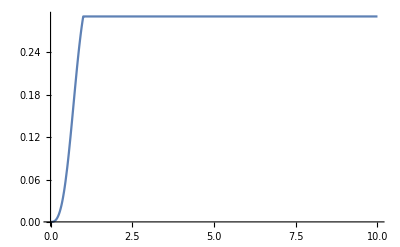

```mathematica
Plot[Evaluate[deltarho[r]/.ans],{r,0,Rmax}]
```

Now that it seems to be working, try plots of the k Cot[δ] and δ for two different depths.  How do you explain the results in terms of Levinson’s theorem?

```mathematica
V0 = 1.;
```

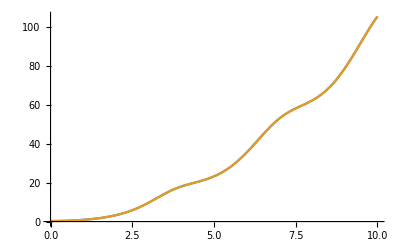

```mathematica
Plot[{k Cot[deltaAnalytic[k,V0]],k Cot[deltaVPA[k,V0]]},{k,0,10},PlotRange->Full]  (* Check that both plots are really here! *)
```

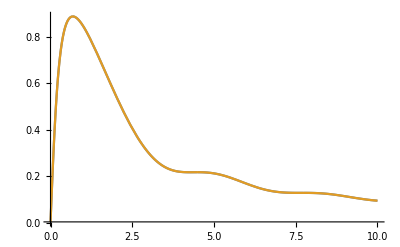

```mathematica
Plot[{deltaAnalyticAdjusted[k,V0],deltaVPA[k,V0]},{k,0.001,10},PlotRange->Full]
```

```mathematica
V0 = 2.;
```

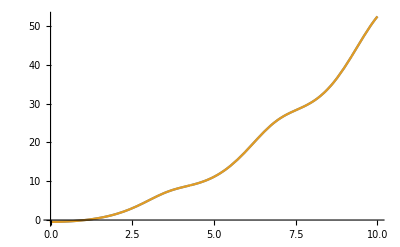

```mathematica
Plot[{k Cot[deltaAnalytic[k,V0]],k Cot[deltaVPA[k,V0]]},{k,0,10},PlotRange->Full]  (* Check that both plots are really here! *)
```

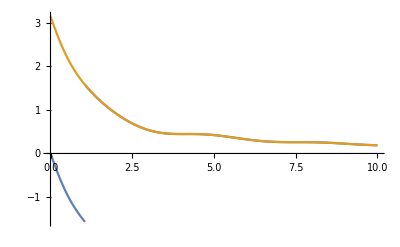

```mathematica
Plot[{deltaAnalyticAdjusted[k,V0],deltaVPA[k,V0]},{k,0.001,10},PlotRange->Full]
```

## Now it’s time to play!

Check whether Levinson’s theorem holds by calculating phase shifts for increasing depths V0 and noting the jump to δ(0) = nπ, where n is the number of bound states (found, for example, from the square_well_example.nb notebook).

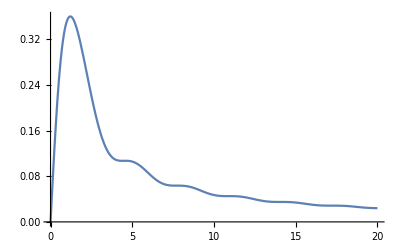
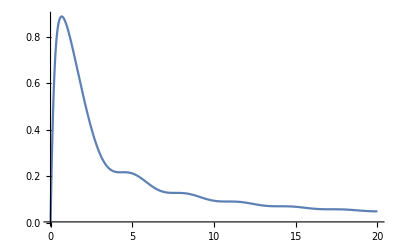
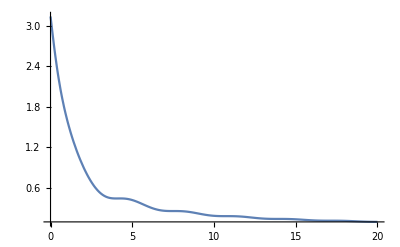
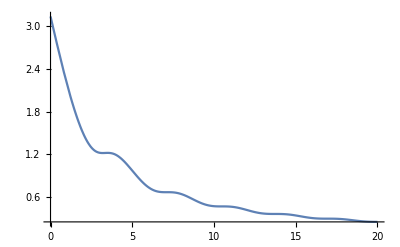
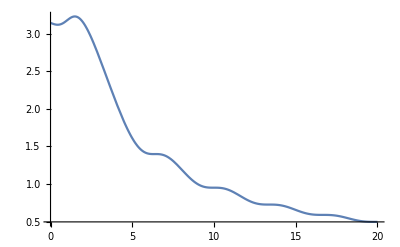
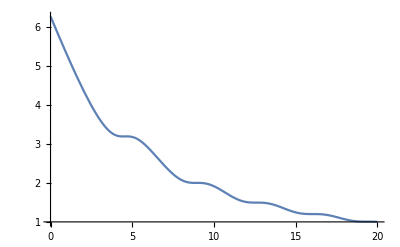

```mathematica
Table[Plot[{deltaVPA[k,V0]},{k,0.001,20},PlotRange->Full],{V0,{0.5,1.0,2.0,5.0,10.0,20.0}}] (* Try for V0 = 0.5 to 20 *)
```

Does it works?  [Note: we start at k=0.001 to avoid numerical issues at k=0.]

This is really fun using Manipulate!

```mathematica
Manipulate[Plot[deltaVPA[k,V0],{k,0.001,10},PlotRange->Full],{V0,0,20,Appearance->"Labeled"}]
```

Verify that the threshold bound state appears at the V0 corresponding to the jump in δ(0).
Check that these two formulas are correct:

```mathematica
1/(2μ)(Pi/(2R))^2 //N  (* Value of V0 for a single bound state at E=0 *)
```

```mathematica
1/(2μ)(3Pi/(2R))^2 //N  (* Value of V0 for two bound states at E=0 *)
```

Check that k Cot[δ] behaves as expected (and Cot[δ] close to a zero-energy bound state):

```mathematica
Manipulate[Plot[k Cot[deltaVPA[k,V0]],{k,0.001,.2},PlotRange->Full],{V0,0,20,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[ Cot[deltaVPA[k,V0]],{k,0.001,.2},PlotRange->Full],{V0,0,20,Appearance->"Labeled"}]
```

## Other potentials . . .

Add a short-range repulsive square well:

```mathematica
Vdoublesw[r_,V0_, Vc_,Rc_] := (Vc+V0) HeavisideTheta[Rc-r]-V0 HeavisideTheta[R-r]  (* Define the square well *)
```

```mathematica
Plot[Vdoublesw[r,5,10,.2],{r,0,5},Exclusions->None]
```

```mathematica
deltaVPAdoublesw[k_,V0_, Vc_,Rc_] :=(
Rmax = 10; (* integrate out to Rmax; just need Rmax > R for square well *)ans = NDSolve[{deltarho'[r]==-(1/k)2μ Vdoublesw[r,V0 ,Vc,Rc] Sin[k r + deltarho[r]]^2,deltarho[0]==0},deltarho,{r,0,Rmax}];
(deltarho[r] /. ans)[[1]] /. r->Rmax 
)
```

```mathematica
Manipulate[Plot[deltaVPAdoublesw[k,V0,Vc,Rc],{k,0.001,10},PlotRange->{-Pi,Pi}],{{V0,5},0,20,Appearance->"Labeled"},{{Vc,0},0,100,Appearance->"Labeled"},{{Rc,.2},0,20,Appearance->"Labeled"}]
```

Start with the repulsive well at zero height and then see what happens when you increase it (go up to 100 eventually).